```mathematica
(*Problem 2: Computation of expected First Passage Time (FPT) of a LIF neuron. *)
lower = -100; upper = 20;
sol = DSolve[{A T'[x]+1/2 B T''[x] == -1, {T[upper]==0,T[lower]==0}},T[x], x]//Simplify
```

{{T[x]→-(100-120 ⅇ^(40-2 x)-ⅇ^240 (-20+x)+x)/(1-ⅇ^240)}}

```mathematica
A = 1; B =1;
```

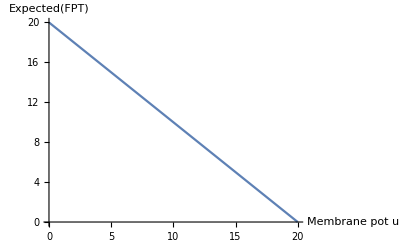

```mathematica
Plot[T[x]/.sol/.{C->20},{x,0,upper},PlotRange->All,AxesLabel->{Membrane pot (u), Expected[FPT]}]
```